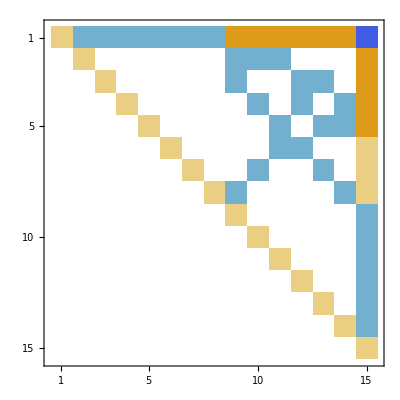

```mathematica
MobiusM//MatrixPlot
```

```mathematica
Inverse[MobiusM]==ZetaM
```

True

```mathematica
VertexList[four]
```

{n1234,n1x234,n134x2,n124x3,n123x4,n14x23,n13x24,n12x34,n1x2x34,n1x24x3,n1x23x4,n14x2x3,n13x2x4,n12x3x4,n1x2x3x4}

```mathematica
vect=Table[Coefficient[allGraphs[1,"colofourrealnull"],v],{v,VertexList[four]}]
```

{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1}

```mathematica
vect2={0,0,0,0,0,0,0,0,1,0,0,0,0,0,1}
```

{0,0,0,0,0,0,0,0,1,0,0,0,0,0,1}

```mathematica
vect.MobiusM
```

{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,2}

```mathematica
({1,0,0,0,0,0,0,0,1,0,0,0,0,0,0}.ZetaM).VertexList[four]
```

n1234+n123x4+n124x3+n12x34+n12x3x4+n134x2+n13x24+n13x2x4+n14x23+n14x2x3+n1x234+n1x23x4+n1x24x3+2 n1x2x34+2 n1x2x3x4

```mathematica
allGraphs[1,"graph"]
```

-Graphics-

```mathematica
allGraphs[1,"colofourrealnull"]
```

-n1x2x34+n1x2x3x4

```mathematica
allGraphs[1,"colofour"]
```

v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4

```mathematica
vect.MobiusM.VertexList[four]
```

-n1x2x34+2 n1x2x3x4

```mathematica
ZetaM.vect.VertexList[four]
```

n123x4+n124x3+n12x3x4+n13x24+n13x2x4+n14x23+n14x2x3+n1x23x4+n1x24x3+n1x2x3x4

```mathematica
LinearSolve[MobiusM ,Table[Indexed[x,i],{i,15}]]
```

{x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12+x13+x14+x15,x2+x9+x10+x11+x15,x3+x9+x12+x13+x15,x4+x10+x12+x14+x15,x5+x11+x13+x14+x15,x6+x11+x12+x15,x7+x10+x13+x15,x8+x9+x14+x15,x9+x15,x10+x15,x11+x15,x12+x15,x13+x15,x14+x15,x15}

```mathematica
LinearSolve[ZetaM ,vect2]
```

{-4,1,1,2,2,1,1,0,0,-1,-1,-1,-1,-1,1}

```mathematica
MakeOne[mat_]:=Map[Map[If[#==0,0,1]&,#]&,mat]
```

```mathematica
MakeOne[MatrixPower[AdjacencyMatrix[four]+IdentityMatrix[15],15]]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
AdjacencyMatrix[four]+IdentityMatrix[15]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixPower[AdjacencyMatrix[four]+IdentityMatrix[15],15]//MatrixForm
```